```mathematica
μm = 10^-6;
μs=10^-6;
ns = 10^-9;
mm=10^-3;
Tera=10^12;
kHz=10^3;
Mega=10^6;
Giga = 10^9;
byte=8;

bpp=10; (*bits per pixel*)
Δx=0.3μm;(*resolution*)
Lz=0.5mm;(*section thickness*)
Ltile=0.5mm;(*tile size*)
freq=8 kHz;(*resonant scanner frequency*)
dwell=(freq Ltile/Δx)^-1
```

7.5×10^-8

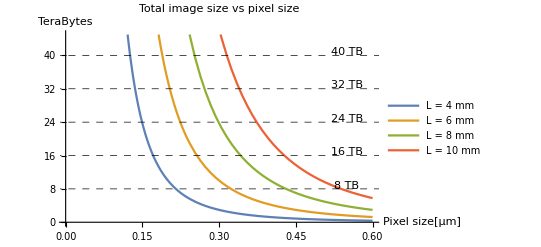

```mathematica
DataSize[L_,Δx_]:=(L/Δx)^3*bpp (*in bits*)
Plot[Evaluate[Table[DataSize[dummy mm,dummy2 μm],{dummy2,0.3,0.6,0.1}]/(Tera*byte)],{dummy,0,10},PlotLegends-> {"pixel size = 0.3 μm","pixel size = 0.4 μm","pixel size = 0.5 μm","pixel size = 0.6 μm"},AxesLabel->{"length[mm]","TeraBytes"},PlotRange->{0,20},GridLines->{{},{8,16}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Data size vs sample size"];

Show[Plot[Evaluate[Table[DataSize[dummy mm,dummy2 μm],{dummy,4,10,2}]/(Tera*byte)],{dummy2,0.1,0.6},AxesOrigin->{0,0},PlotRange->{0,45},PlotLegends-> {"L = 4 mm","L = 6 mm","L = 8 mm","L = 10 mm"},AxesLabel->{"Pixel size[μm]","TeraBytes"},GridLines->{{},{8,16,24,32,40}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Total image size vs pixel size"],Graphics[Table[Text[ToString[i]"TB",{0.55,i+.8}],{i,8,40,8}]]]
```

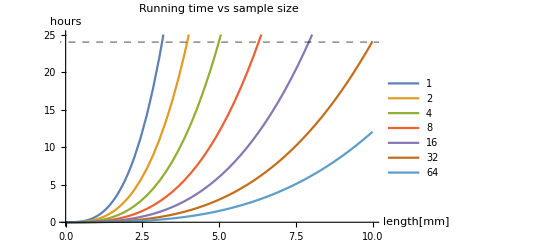

```mathematica
time[L_,α_]:=(L/Δx)^3 dwell/α(*total running time*)
Plot[Evaluate[Table[time[dummy mm,2^i]/3600,{i,0,6}]],{dummy,0,10},PlotRange->{0,25},AxesLabel->{"length[mm]","hours"},PlotLegends->Table[2^i,{i,0,6}],GridLines->{{},{24}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Running time vs sample size"]

time[L_,α_]:=(L/Δx)^3 dwell/α(*total run time*)
Show[Plot[Evaluate[Table[time[dummy mm,dummy2]/3600,{dummy,4,10,2}]],{dummy2,1,64},PlotRange->{{1,64},{0,25}},AxesOrigin->{1,0},AxesLabel->{"multiplexing factor","hours"},GridLines->{{},{24}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Run time vs multiplexing factor",PlotLegends-> {"L = 4 mm","L = 6 mm","L = 8 mm","L = 10 mm"}],Graphics[Text["1 day",{58,22}]]];
```

```mathematica
L=10mm;
NumTiles = (L/Ltile)^2(*number of tiles*)
NumSections=L/Lz
NumPixels=(L/Δx)^3(*number of pixels*)
```

400.

20.

3.7037×10^13

```mathematica
1/dwell*bpp/(Mega*byte)(*data-saving speed in MB/seconds PER BEAMLET. A commercial HDD writes at 150 MB/s*)
```

16.6667

```mathematica
HDD=(8 Tera)*byte (*max HDD capacity in bits*)
busrate=10 10^9;(*transfer rate in bps*)
1.*HDD/busrate/3600 (*Time to transfer a 8TB HDD [in hours]*)
```

64000000000000

1.77778

```mathematica
Ltile^2/dwell(*frames per second*)
```

3.33333